```mathematica
(*球面face腔传播程序
输入量：球面半径ρ，腔面变形程度θ0,边界变形程度a2,a3,b2,b3,初始点相位θstart,传播方向spin（顺时针+，逆时针-）,初始点与第二点夹角φ0(由周期数w决定),*)
ρ=10;
θ0=π/9;(*极坐标(ρ,φ,θ)下Face腔基本θ值*)
a2=-0.1329;a3=0.0948;
b2=-0.0642;b3=-0.0224;
θstart=π/3;(*初始点位置选在π相位,0~2π*)
spin=-1;(*旋转方向，顺时针取1，逆时针取-1*)


Table[
Clear[φ,θ,z1,z2,y0,s,d,p,m1,n1,x00,y00,y000,s1,s3,s4];
z3=(z1-z2)+z1;z1=0.5;z2=-4;y0=0.;s=0.98;d=1.8;
p={};(*测地线图*)
q={}; 
         (*SOS点*)

φ0=N[2*π/w,10];(*起始第二点角度*)

(*a2=-0.;a3=0.;
b2=-0.;b3=-0;*)

f1=z-Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+a2*(x/Sqrt[x^2+y^2])^2+a3*(x/Sqrt[x^2+y^2])^3)];
f2=x^2+y^2+z^2-1;
f4=z-Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+b2*(x/Sqrt[x^2+y^2])^2+b3*(x/Sqrt[x^2+y^2])^3)];
f3=z-Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+a2*(x/Sqrt[x^2+y^2])^2+a3*(x/Sqrt[x^2+y^2])^3)];
(*s1=(θ-θ0*(1+a2*(ρ*Sin[θ]*Cos[φ]/(ρ*Sin[θ]))^2+a3*(ρ*Sin[θ]*Cos[φ]/(ρ*Sin[θ]))^3));*)
s2=ρ-1;
s3=(θ-θ0*(1+a2*(ρ*Sin[θ]*Cos[φ]/(ρ*Sin[θ]))^2+a3*(ρ*Sin[θ]*Cos[φ]/(ρ*Sin[θ]))^3));
s4=(θ-θ0*(1+b2*(ρ*Sin[θ]*Cos[φ]/(ρ*Sin[θ]))^2+b3*(ρ*Sin[θ]*Cos[φ]/(ρ*Sin[θ]))^3));


p3=ContourPlot3D[{x^2+y^2+z^2==ρ^2},{x,-ρ,ρ},{y,-ρ,ρ},{z,ρ*Cos[θ0],ρ},BoxRatios->{1, 1, 1},MeshFunctions->{Function[{x,y,z,f},f4-f2]},MeshStyle->{{Thickness[0.1],Blue}},RegionFunction->Function[{x,y,z},(x>0&&z>=Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+a2*(x/Sqrt[x^2+y^2])^2+a3*(x/Sqrt[x^2+y^2])^3)])||(x≤0&&z>=Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+b2*(x/Sqrt[x^2+y^2])^2+b3*(x/Sqrt[x^2+y^2])^3)])],ContourStyle->Directive[Yellow,Opacity[0.5],Specularity[White,30]],Mesh->None,RegionBoundaryStyle->None];
(*p3=ContourPlot3D[{f3==0,f2==0},{x,-1,1},{y,-1,1},{z,-1,1},MeshFunctions->{Function[{x,y,z,f},f3-f2]},MeshStyle->{{Thickness[0.001],Blue}},Mesh->{{0}},ContourStyle->Directive[Blue,Opacity[0.2],Specularity[White,30]]];
p4=ContourPlot3D[{f4==0,f2==0},{x,-1,1},{y,-1,1},{z,-1,1},MeshFunctions->{Function[{x,y,z,f},f4-f2]},MeshStyle->{{Thickness[0.001],Blue}},Mesh->{{0}},ContourStyle->Directive[Blue,Opacity[0.2],Specularity[White,30]]];(*腔边界突出*)*)


{m1,n1}=NSolve[(s3==0)&&ρ*Sin[θ]*Cos[φ]==0&&0<θ<π&&0<=φ<2π,{θ,φ},Reals,WorkingPrecision->30];


x00=N[{x->ρ*Sin[θ]*Cos[φ],y->ρ*Sin[θ]*Sin[φ],z->ρ*Cos[θ]}/.m1,20];(*边界判断条件点*)

x000=N[Abs[ρ*Sin[θ]*Sin[φ]/.m1],20];(*边界判断条件量*)

(*x0={ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.If[(ρ*Sin[θ]*Sin[φ]/.m1)<0,m1,n1];(*初始点 3π/2 *)*)
g0={0,1,0};
θstart=θstart;(*初始点位置选在π相位,0~2π*)
s1=If[Cos[θstart]>=0,s3,s4];(*根据初始点位置决定边界方程s3/s4*)
g0={Cos[θstart+π/2],Sin[θstart+π/2],0};
{m1,n1}=Solve[(s1==0)&&(g0.{ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]})==0&&0<θ<π&&0<=φ<2π,{θ,φ},Reals];  
 x0={ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.If[(Norm[θstart-φ/.m1])<Norm[θstart-φ/.n1],m1,n1];(*方位角θstart决定的初始点坐标，*Cos[]自动*)


spin=spin;(*旋转方向，顺时针取1，逆时针取-1*)
(*g={Cos[π/2-φ0],Sin[π/2-φ0],0};(*更换初始点，相应改变入射点位置，φ0是旋转周期数角度，初始点位置为θ1,g的角度选取为π/2+φ0,逆时针整体取负，现在初始点为π，逆时针，所以为-(π/2+φ0+π)*)*)
g={Cos[θstart+π/2+spin*φ0],Sin[(θstart+π/2+spin*φ0)],0};(*更换初始点，相应改变入射点位置，φ0是旋转周期数角度，初始点位置为θstart,g的角度选取为π/2+φ0,逆时针整体取负，逆时针，所以为-(π/2+φ0+θstart)*)
(*Print[θstart+π/2+φ0,φ0,g];*)
If[Cos[θstart+spin*φ0]>0,s1=s3,s1=s4];

{m1,n1}=Solve[(s1==0)&&(g.{ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]})==0&&0<θ<π&&0<=φ<2π,{θ,φ},Reals];  
 x1={ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.If[(ρ*Sin[θ]*Sin[φ]/.m1)*Sin[θstart+spin*φ0]>0,m1,n1];(*选取入射点,Sin[初始角度+/-第二点角度]，顺时针为正，逆时针取负*)


(*Print[ArcCos[x1[[1]]/(x1[[1]]^2+x1[[2]]^2)^0.5]/(2π)];(*输出入射点方位角*)*)
fx=D[f2,x];fy=D[f2,y];fz=D[f2,z];(*球面法向参数*)
hx={D[f3,x],D[f4,x]};hy={D[f3,y],D[f4,y]};hz={D[f3,z],D[f4,z]};(*柱面法向参数*)

Table[
Clear[y00,y000];
g=Cross[x0,x1];g=g/Norm[g];(*1.测地平面法向量*)

y00=Abs[NSolve[g.({x,y000,z}/.x00)==0,y000,Reals][[1]][[1]][[2]]];(*新光线在z高度的y截距*)
(*Print[y00,x0];*)



If[(*Chop[x0[[1]]]==0&&x0[[2]]*spin<0 )||*)(x0[[1]]>0&&y00>=x000)||(x0[[1]]<0&&y00<x000),(f1=f3;s1=s3;f=1),(f1=f4;s1=s4;f=2)];
If[((*N[y00,8]==x000 &&*)Chop[x0[[1]]]==0),(If[x0[[2]]*spin<0,(f1=f3;s1=s3;f=1;),(f1=f4;s1=s4;f=2;)])];(*修正π/2与3π/2初始位置时的边界选择错误，错误原因在于初始点横坐标不完全等于0*)



(*If[Abs[y00=y00/.Solve[g.({x,y00,z}/.x00)==0,y00][[1]]]<Abs[y/.x00],f1=Complement[{f1,
f3},{f1}][[1]],f1=f1];*)(*判断反射边界*)
{m1,n1}=Solve[s1==0&&g.{ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}==0&&0<=θ<=π&&0<=φ<2π,{θ,φ},Reals];
(*Print[s1,f];*)
x2={x->ρ*Sin[θ]*Cos[φ],y->ρ*Sin[θ]*Sin[φ],z->ρ*Cos[θ]}/.If[Norm[({ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.m1)-x0]>Norm[({ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.n1)-x0],m1,n1];(*2.第二点*)


t1=(*{fy*g[[3]]-fz*g[[2]],-fx*g[[3]]+fz*g[[1]],fx*g[[2]]-fy*g[[1]]}/.x2;*)Cross[g,{x,y,z}/.x2];t1=t1/Norm[t1];(*3.第二点处入射切向量*)
(*hx=D[f1,x];hy=D[f1,y];hz=D[f1,z];(*柱面法向参数*)*)
n={fy*hz[[f]]-fz*hy[[f]],-fx*hz[[f]]+fz*hx[[f]],fx*hy[[f]]-fy*hx[[f]]}/.x2;(*4.边界第二点切向量，雅克比行列式*)



{m1,n1}=Solve[{j,k,l}.n==t1.n&&({x,y,z}/.x2).{j,k,l}==0&&Norm[{j,k,l}]==1,{j,k,l},Reals];

t2=If[({j,k,l}/.m1).t1>({j,k,l}/.n1).t1,n1,m1];(*5.第二点反射切向量*)
If[Chop[n[[1]]]==0,t2=FindRoot[{Norm[{j,k,l}]==1,{j,k,l}.n-t1.n==0,({x,y,z}/.x2).{j,k,l}==0},{{j,-t1[[1]]},{k,0},{l,0}}]];(*针对0，π位置反射光线方向有误，排查问题发现问题出在求解反射向量t2的solve函数中，求解结果不满足模值为1的设定，在此添加条件判断当边界切线横坐标值为0时（即0，π位置），使用findroot函数直接在t1对称方向重新寻找t2*)


fp=RotationTransform[{{0,0,1}*ρ,g*ρ}][{ρ*Cos[u],ρ*Sin[u],0}];
p2=ParametricPlot3D[fp,{u,0,2π},PlotStyle->{Black,Thickness[0.002]},PlotPoints->50,RegionFunction->Function[{x,y,z},x>0&&z>=Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+a2*(x/Sqrt[x^2+y^2])^2+a3*(x/Sqrt[x^2+y^2])^3)]||x≤0&&z>=Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+b2*(x/Sqrt[x^2+y^2])^2+b3*(x/Sqrt[x^2+y^2])^3)]]];p=Append[p,p2];(*测地线作图*)
θx=If[(y/.x2)>=0,ArcCos[(x/.x2)/((x/.x2)^2+(y/.x2)^2)^0.5]/(2π),(2π-ArcCos[(x/.x2)/((x/.x2)^2+(y/.x2)^2)^0.5])/(2π)];
(*θx=If[θx>0.75,θx-0.75,θx+0.25];*)
sinψ=Abs[Cos[VectorAngle[t1,n]]];q=Append[q,{θx,sinψ}];

x0={x,y,z}/.x2;x1={j,k,l}/.t2,
{o,1,500}];(*Print[sinψ];*)
{},{w,{3.3}}]



Show[p,p3,PlotRange->{{-ρ*Sin[θ0],ρ*Sin[θ0]},{-ρ*Sin[θ0],ρ*Sin[θ0]},{ρ*Cos[θ0],ρ}}]
(*bug记录：
初始点选在π/2，顺时针边界选择有问题，逆时针只有第二点在0时出射光线方向不对,3π/2的位置，逆时针边界选择有问题，顺时针出射光线有问题
约化x0坐标后，边界选择没有问题，但在0，π位置反射光线方向不对
chop函数近似取零后只在0，π位置反射光线方向不对*)
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{}}

-Graphics3D-

```mathematica
p={};
Table[
Clear[y00,y000];
g=Cross[x0,x1];g=g/Norm[g];(*1.测地平面法向量*)

y00=Abs[NSolve[g.({x,y000,z}/.x00)==0,y000,Reals][[1]][[1]][[2]]];(*新光线在z高度的y截距*)
(*Print[y00,x0];*)



If[(*Chop[x0[[1]]]==0&&x0[[2]]*spin<0 )||*)(x0[[1]]>0&&y00>=x000)||(x0[[1]]<0&&y00<x000),(f1=f3;s1=s3;f=1),(f1=f4;s1=s4;f=2)];
If[((*N[y00,8]==x000 &&*)Chop[x0[[1]]]==0),(If[x0[[2]]*spin<0,(f1=f3;s1=s3;f=1;),(f1=f4;s1=s4;f=2;)])];(*修正π/2与3π/2初始位置时的边界选择错误，错误原因在于初始点横坐标不完全等于0*)



(*If[Abs[y00=y00/.Solve[g.({x,y00,z}/.x00)==0,y00][[1]]]<Abs[y/.x00],f1=Complement[{f1,
f3},{f1}][[1]],f1=f1];*)(*判断反射边界*)
{m1,n1}=Solve[s1==0&&g.{ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}==0&&0<=θ<=π&&0<=φ<2π,{θ,φ},Reals];
(*Print[s1,f];*)
x2={x->ρ*Sin[θ]*Cos[φ],y->ρ*Sin[θ]*Sin[φ],z->ρ*Cos[θ]}/.If[Norm[({ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.m1)-x0]>Norm[({ρ*Sin[θ]*Cos[φ],ρ*Sin[θ]*Sin[φ],ρ*Cos[θ]}/.n1)-x0],m1,n1];(*2.第二点*)


t1=Cross[g,{x,y,z}/.x2];t1=t1/Norm[t1];(*3.第二点处入射切向量*)
(*hx=D[f1,x];hy=D[f1,y];hz=D[f1,z];(*柱面法向参数*)*)
n={fy*hz[[f]]-fz*hy[[f]],-fx*hz[[f]]+fz*hx[[f]],fx*hy[[f]]-fy*hx[[f]]}/.x2;(*4.边界第二点切向量，雅克比行列式*)



{m1,n1}=Solve[{j,k,l}.n==t1.n&&({x,y,z}/.x2).{j,k,l}==0&&Norm[{j,k,l}]==1,{j,k,l},Reals];

t2=If[({j,k,l}/.m1).t1>({j,k,l}/.n1).t1,n1,m1];(*5.第二点反射切向量*)
If[Chop[n[[1]]]==0,t2=FindRoot[{Norm[{j,k,l}]==1,{j,k,l}.n-t1.n==0,({x,y,z}/.x2).{j,k,l}==0},{{j,-t1[[1]]},{k,0},{l,0}}]];(*针对0，π位置反射光线方向有误，排查问题发现问题出在求解反射向量t2的solve函数中，求解结果不满足模值为1的设定，在此添加条件判断当边界切线横坐标值为0时（即0，π位置），使用findroot函数直接在t1对称方向重新寻找t2*)


fp=RotationTransform[{{0,0,1}*ρ,g*ρ}][{ρ*Cos[u],ρ*Sin[u],0}];
p2=ParametricPlot3D[fp,{u,0,2π},PlotStyle->{Black,Thickness[0.002]},PlotPoints->50,RegionFunction->Function[{x,y,z},x>0&&z>=Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+a2*(x/Sqrt[x^2+y^2])^2+a3*(x/Sqrt[x^2+y^2])^3)]||x≤0&&z>=Sqrt[x^2+y^2+z^2]*Cos[θ0*(1+b2*(x/Sqrt[x^2+y^2])^2+b3*(x/Sqrt[x^2+y^2])^3)]]];p=Append[p,p2];(*测地线作图*)
θx=If[(y/.x2)>=0,ArcCos[(x/.x2)/((x/.x2)^2+(y/.x2)^2)^0.5]/(2π),(2π-ArcCos[(x/.x2)/((x/.x2)^2+(y/.x2)^2)^0.5])/(2π)];
(*θx=If[θx>0.75,θx-0.75,θx+0.25];*)
sinψ=Abs[Cos[VectorAngle[t1,n]]];q=Append[q,{θx,sinψ}];

x0={x,y,z}/.x2;x1={j,k,l}/.t2,
{o,1,1000}];//AbsoluteTiming
Show[p,p3,PlotRange->{{-ρ*Sin[θ0],ρ*Sin[θ0]},{-ρ*Sin[θ0],ρ*Sin[θ0]},{ρ*Cos[θ0],ρ}}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{143.207,Null}

-Graphics3D-

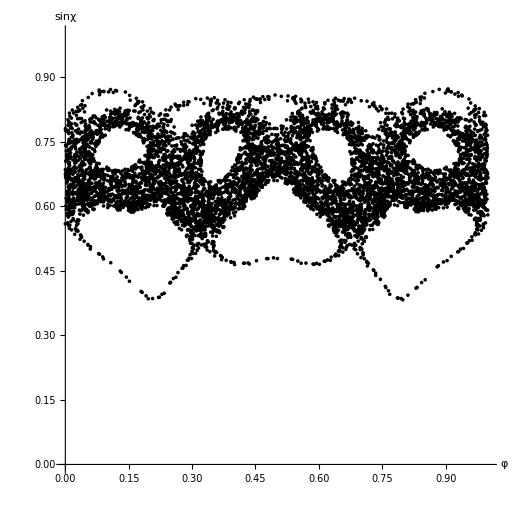

```mathematica
ListPlot[q,PlotStyle->{PointSize[0.005],Black},AxesLabel->{Style[φ,15],Style[sinχ,15]} ,PlotRange->{0,1},AspectRatio->1]
```

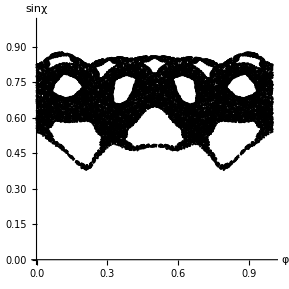
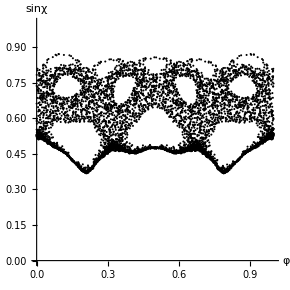
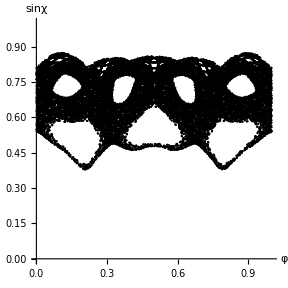
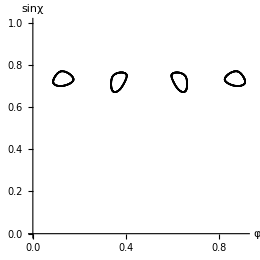
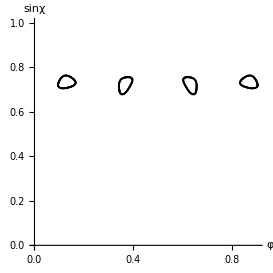
```mathematica
θ0=π/9,
-Graphics-θstart=π/3,w=3.4,chaos no end .-Graphics-θstart=π/3,w=3.5,final down the  island 3 .-Graphics-θstart=π/3,w=3.6,final in island 5.-Graphics-θstart=π/3,w=3.7,trapped in island 4 directly.-Graphics-θstart=π/3,w=3.8,trapped in island 4.
```

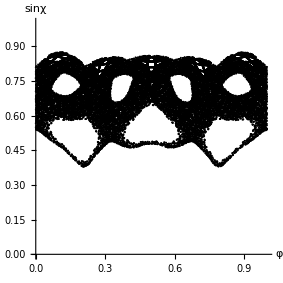
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,PlotStyle->{PointSize[0.005],White}]
```